En los siguientes problemas, dibuja el espacio fase, encuentra las soluciones de equilibrio, determina su estabilidad y dibuja las soluciones como función de t de manera cualitativamente correcta.

y'=y(1-y)(2-y)

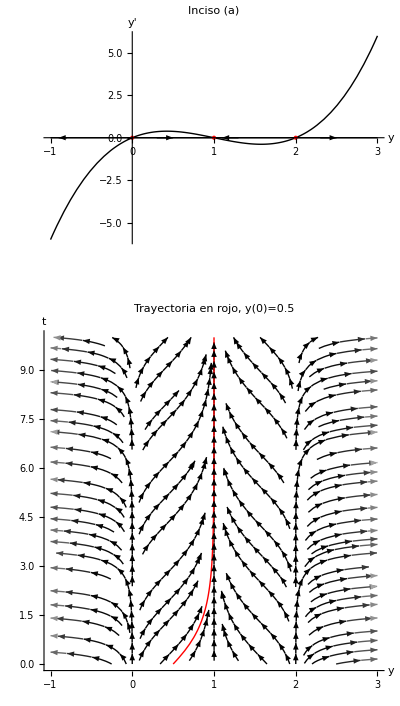

```mathematica
ClearAll["Global`*"]
Module[
  {f, yMin, yMax, tMax, plotYprime, dirField, sol, solCurve},
  
  (* y' = y (1-y)(2-y) *)
  f[y_] := y (1 - y) (2 - y);
  
  (* Rango para y y t *)
  yMin = -1; yMax = 3;
  tMax = 10;
  
  (************************************************************)
  (* 1) Gráfica de y'(y) + Diagrama de Fases (arriba)         *)
  (************************************************************)
  plotYprime = Plot[
    f[y],
    {y, yMin, yMax},
    AxesLabel -> {"y", "y'"},
    PlotLabel -> "Inciso (a)",
    PlotRange -> {{yMin, yMax}, All},
    PlotStyle -> Thick,
    Epilog -> {
      (* Recta y'=0 *)
      Thick, Line[{{yMin, 0}, {yMax, 0}}],
      
      (* Equilibrios y=0,1,2 *)
      {Red, PointSize[Large],
       Point[{{0, 0}, {1, 0}, {2, 0}}]},
      
      (* Flechas de fase *)
      Arrow[{{-0.8, 0}, {-0.9, 0}}],  (* a la izq, f<0 *)
      Arrow[{{0.3, 0}, {0.5, 0}}],    (* a la der, f>0 *)
      Arrow[{{1.3, 0}, {1.1, 0}}],    (* a la izq, f<0 *)
      Arrow[{{2.3, 0}, {2.5, 0}}]     (* a la der, f>0 *)
    },
    ImageSize -> 400
  ];
  
  (************************************************************)
  (* 2) Campo de pendientes (y horizontal, t vertical)        *)
  (*    + trayectoria en rojo (abajo)                          *)
  (************************************************************)
  dirField = StreamPlot[
    {f[y], 1},   (* (dx, dy) = (f(y), 1) en coords (y,t) *)
    {y, yMin, yMax}, {t, 0, tMax},
    StreamStyle -> Arrowheads[Small],
    (* Para que aparezcan ejes tradicionales: *)
    Axes -> True, Frame -> False,
    AxesLabel -> {"y", "t"},
    PlotLabel -> "Campo de pendientes en (y,t)",
    PlotRange -> All,
    ImageSize -> 400
  ];
  
  (* Resolvemos la ODE con y(0)=0.5 *)
  sol = First@NDSolve[
    {y'[t] == f[y[t]], y[0] == 0.5},
    y, {t, 0, tMax}
  ];
  
  (* Trayectoria paramétrica: (y(t), t) *)
  solCurve = ParametricPlot[
    Evaluate[{y[t] /. sol, t}],
    {t, 0, tMax},
    PlotStyle -> {Thick, Red},
      (* evitamos ejes dobles *)
    PlotRange -> All
  ];
  
  (* Fusionamos dirField y solCurve con PlotRange->All *)
  GraphicsColumn[
    {
      plotYprime,
      Show[
        dirField,
        solCurve,
        PlotRange -> All,
        PlotLabel -> "Trayectoria en rojo, y(0)=0.5"
      ]
    },
    Alignment -> Center
  ]
]
```

y'=y^2(y+1)

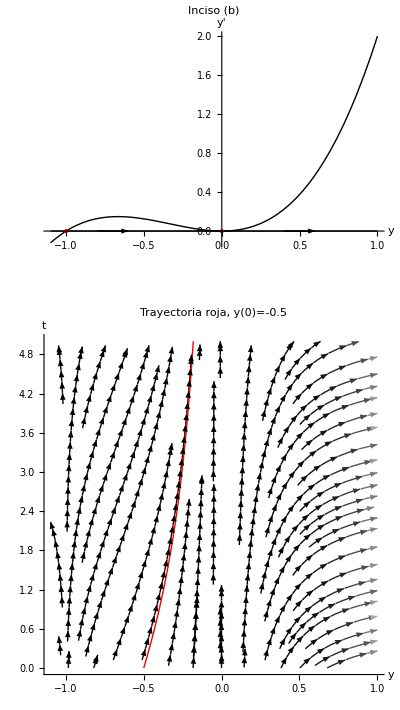

```mathematica
ClearAll["Global`*"]
Module[
  {g, yMin, yMax, tMax, plotYprime, dirField, sol, solCurve},
  
  (* y' = y^2 (y+1) *)
  g[y_] := y^2 (y + 1);
  
  yMin = -1.1; yMax = 1;
  tMax = 5;
  
  (************************************************************)
  (* 1) y'(y) + Diagrama de Fases (arriba)                     *)
  (************************************************************)
  plotYprime = Plot[
    g[y],
    {y, yMin, yMax},
    AxesLabel -> {"y", "y'"},
    PlotLabel -> "Inciso (b)",
    PlotRange -> {{yMin, yMax}, All},
    PlotStyle -> Thick,
    Epilog -> {
      Thick, Line[{{yMin, 0}, {yMax, 0}}],
      {Red, PointSize[Large],
       Point[{{-1, 0}, {0, 0}}]},
      Arrow[{{-1.8, 0}, {-1.6, 0}}],
      Arrow[{{-0.8, 0}, {-0.6, 0}}],
      Arrow[{{0.4, 0}, {0.6, 0}}]
    },
    ImageSize -> 400
  ];
  
  (************************************************************)
  (* 2) Campo de pendientes (y horizontal, t vertical)         *)
  (*    + trayectoria roja (abajo)                             *)
  (************************************************************)
  dirField = StreamPlot[
    {g[y], 1},
    {y, yMin, yMax}, {t, 0, tMax},
    StreamStyle -> Arrowheads[Small],
    Axes -> True, Frame -> False,
    AxesLabel -> {"y", "t"},
    PlotLabel -> "Campo de pendientes en (y,t)",
    PlotRange -> All,
    ImageSize -> 400
  ];
  
  (* ODE con y(0)= -0.5, por ejemplo *)
  sol = First@NDSolve[
    {y'[t] == g[y[t]], y[0] == -0.5},
    y, {t, 0, tMax}
  ];
  
  (* (y(t), t) en ParametricPlot *)
  solCurve = ParametricPlot[
    Evaluate[{y[t] /. sol, t}],
    {t, 0, tMax},
    PlotStyle -> {Thick, Red},
    Axes -> None,
    PlotRange -> All
  ];
  
  GraphicsColumn[
    {
      plotYprime,
      Show[
        dirField,
        solCurve,
        PlotRange -> All,
        PlotLabel -> "Trayectoria roja, y(0)=-0.5"
      ]
    },
    Alignment -> Center
  ]
]
```

y'=r y (K-y)/(K+A y)

```mathematica
ClearAll["Global`*"]
Manipulate[
  Module[
    {f, yMin = -0.2, yMax, tMax = 5, plotYprime, dirField, sol, solCurve},
    
    (* Definimos f(y) con los sliders de r,K,A *)
    f[y_] := r * y * (K - y) / (K + A y);
    
    (* Tomamos yMax como 3*K para visualizar mas alla de K *)
    yMax = 3 K;
    
    (************************************************************)
    (* 1) Gráfica y'(y) + diagrama de fases                    *)
    (************************************************************)
    plotYprime = Plot[
      f[y],
      {y, yMin, yMax},
      AxesLabel -> {"y", "y'"},
      PlotLabel -> "Inciso (c)",
      PlotRange -> All,
      PlotStyle -> Thick,
      Epilog -> {
        Thick, Line[{{yMin, 0}, {yMax, 0}}],
        {Red, PointSize[Large],
         Point[{{0, 0}, {K, 0}}]},
        (* Flechas: en (0,K) -> f>0 (der), en (K,yMax) -> f<0 (izq) *)
        Arrow[{{0.3 K, 0}, {0.5 K, 0}}],
        Arrow[{{1.3 K, 0}, {1.1 K, 0}}]
      },
      ImageSize -> 400
    ];
    
    (************************************************************)
    (* 2) Campo de pendientes (y,t) + trayectoria roja          *)
    (************************************************************)
    dirField = StreamPlot[
      {f[y], 1},
      {y, yMin, yMax}, {t, -0.2, tMax},
      StreamStyle -> Arrowheads[Small],
      Axes -> True, Frame -> False,
      AxesLabel -> {"y", "t"},
      PlotLabel -> "Campo de pendientes (y horizontal, t vertical)",
      PlotRange -> All,
      ImageSize -> 400
    ];
    
    (* Resolvemos la ODE con y(0)=y0 *)
    sol = First@NDSolve[
      {y'[t] == f[y[t]], y[0] == y0},
      y, {t, 0, tMax}
    ];
    
    (* Graficamos la trayectoria: ( y(t), t ) *)
    solCurve = ParametricPlot[
      Evaluate[{y[t] /. sol, t}],
      {t, 0, tMax},
      PlotStyle -> {Thick, Red},
      Axes -> None,
      PlotRange -> All
    ];
    
    GraphicsColumn[
      {
        plotYprime,
        Show[
          dirField,
          solCurve,
          PlotRange -> All,
          PlotLabel -> "Trayectoria roja, y(0) = " <> ToString[y0]
        ]
      },
      Alignment -> Center
    ]
  ],
  
  {{r, 1, "r"}, 0.1, 5, Appearance -> "Labeled"},
  {{K, 2, "K"}, 0.1, 5, Appearance -> "Labeled"},
  {{A, 0.5, "A"}, 0.1, 5, Appearance -> "Labeled"},
  {{y0, 1, "y(0)"}, 0, 5, Appearance -> "Labeled"}
]
```